```mathematica
Table[{base1,base2,ConversionMatrix[base1,base2]//Det},{base1,allBases},{base2,allBases}]
```

{{{C,C,1},{C,E,1},{C,G,1},{C,F,-1/96}},{{E,C,1},{E,E,1},{E,G,1},{E,F,-1/96}},{{G,C,1},{G,E,1},{G,G,1},{G,F,-1/96}},{{F,C,-96},{F,E,-96},{F,G,-96},{F,F,1}}}

```mathematica
TopVars[k_]:=Block[{vars=ListofVars[allGraphs5[k,"colofour"]],topLevel},
topLevel=Max[Map[SymbolLevel,vars]];
Select[vars,SymbolLevel[#]==topLevel&]
]
```

```mathematica
BottomVars[k_]:=Block[{vars=ListofVars[allGraphs5[k,"colofour"]],topLevel},
topLevel=Min[Map[SymbolLevel,vars]];
Select[vars,SymbolLevel[#]==topLevel&]
]
```

```mathematica
TopVars2[k_]:=Block[{vars=ListofVars[allGraphs5[k,"colofourrealnull"]],topLevel},
topLevel=Max[Map[SymbolLevel,vars]];
Select[vars,SymbolLevel[#]==topLevel&]
]
```

```mathematica
BottomVars2[k_]:=Block[{vars=ListofVars[allGraphs5[k,"colofourrealnull"]],topLevel},
topLevel=Min[Map[SymbolLevel,vars]];
Select[vars,SymbolLevel[#]==topLevel&]
]
```

```mathematica
TopVars3[k_]:=Block[{vars=ListofVars[allGraphs5[k,"colofournull"]],topLevel},
topLevel=Max[Map[SymbolLevel,vars]];
Select[vars,SymbolLevel[#]==topLevel&]
]
```

```mathematica
BottomVars3[k_]:=Block[{vars=ListofVars[allGraphs5[k,"colofournull"]],topLevel},
topLevel=Min[Map[SymbolLevel,vars]];
Select[vars,SymbolLevel[#]==topLevel&]
]
```

```mathematica
Table[BottomVars2[k],{k,RandomSample[Keys[allGraphs5],100]}]
```

{{n1345x2},{n125x34},{n12345},{n135x24},{n12345},{n12345},{n1234x5},{n145x23},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n1245x3},{n135x24},{n13x2x45},{n12345},{n1235x4},{n12345},{n12345},{n125x3x4},{n12345},{n12345},{n125x34},{n12345},{n12345},{n1235x4},{n12345},{n12345},{n145x23},{n134x25},{n12345},{n125x3x4},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n134x25},{n12345},{n12345},{n12345},{n12345},{n12345},{n1235x4},{n12345},{n135x24},{n12345},{n13x2x4x5},{n15x23x4},{n12345},{n12345},{n12345},{n1234x5},{n12345},{n12345},{n12345},{n12345},{n12345},{n1345x2},{n12345},{n12345},{n12345},{n12345},{n1234x5},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n13x245},{n14x2x35},{n13x245},{n13x245},{n1245x3},{n12345},{n12345},{n12345},{n12345},{n12345},{n12345},{n13x245},{n135x2x4},{n12345},{n12345},{n12345},{n1234x5},{n12345},{n12345},{n123x45}}

```mathematica
Length[Select[Keys[allGraphs5],Length[TopVars3[#]]==1&]]
```

153

```mathematica
Length[Select[Keys[allGraphs5],Length[TopVars[#]]==1&&Length[BottomVars[#]]==1&]]
```

718

```mathematica
MobiusGraph4C[key_,allGraphs_]:=Block[{form=allGraphs[key,"colofour"], vars, blocks=Association[],c,edges,set, found=Association[],realyNullAtomKeys=Sort[Select[Keys[allGraphs],Length[ListofVars[allGraphs[#,"colofour"]]]==1&]],problemSize=Length[allGraphs[0,"vertexsets"]]},
vars=ListofVars[form];

(* initialize all blocks to empty sets *)
Table[blocks[k]={},{k,0,problemSize}];
(* put each base set ion a bucket by length.  In eahc bucket we store the variable and the vertexsets associated with that variable *)
Table[
set=allGraphs[First[Select[realyNullAtomKeys,allGraphs[#,"colofour"]==v&]]];
found [v]=set;
set=set["vertexsets"];
c=Length[set];
blocks[c]=Append[blocks[c],{v,set}]
,{v,vars}
];
(* now compute the edges.
For this we go over all blocks per size.
For each of the "size +1" we add and an edge if the first is a refinement of the second
*)
edges={};
Table[
Table[
Table[
If[IsRefinement[from[[2]],to[[2]]],

AppendTo[edges,DirectedEdge[
to[[1]],
from [[1]]]]
],{to,blocks[k]}
],{from,blocks[k-1]}
]
,{k,1,problemSize}];
Graph[vars,edges,VertexLabels->Table[n->Rotate[(TableForm[{n,Style[Coefficient[form,n],Bold,Blue], Style[DropMore[n,3],Red]},TableAlignments->Center]),Pi/4],{n,vars}],GraphLayout->"LayeredDigraphEmbedding"]
]
```

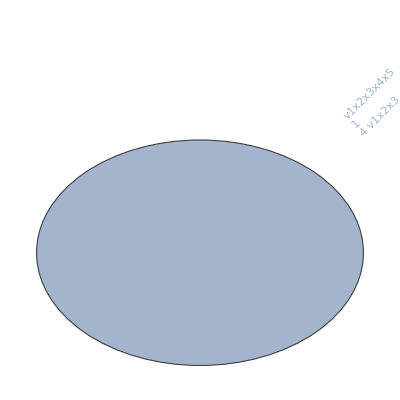
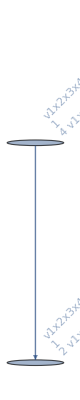
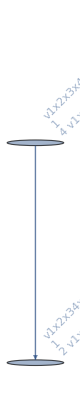
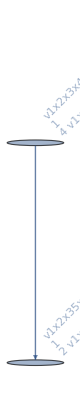
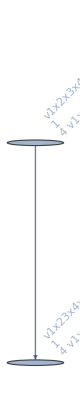
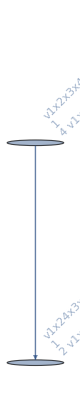
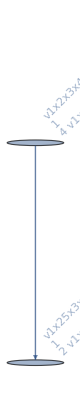
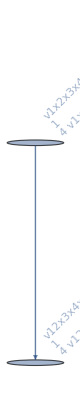
{{-Graphics-,-Graphics-295240}{v1x2x3x4x5,{v1x2x3x4x5},{v1x2x3x4x5}},{-Graphics-,-Graphics-295230}{v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1x2x3x45}},{-Graphics-,-Graphics-295150}{v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v1x2x34x5}},{-Graphics-,-Graphics-295210}{v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v1x2x35x4}},{-Graphics-,-Graphics-292810}{v1x23x4x5+v1x2x3x4x5,{v1x2x3x4x5},{v1x23x4x5}},{-Graphics-,-Graphics-294430}{v1x24x3x5+v1x2x3x4x5,{v1x2x3x4x5},{v1x24x3x5}},{-Graphics-,-Graphics-294970}{v1x25x3x4+v1x2x3x4x5,{v1x2x3x4x5},{v1x25x3x4}},{-Graphics-,-Graphics-98410}{v12x3x4x5+v1x2x3x4x5,{v1x2x3x4x5},{v12x3x4x5}},{-Graphics-,-Graphics-229630}{v13x2x4x5+v1x2x3x4x5,{v1x2x3x4x5},{v13x2x4x5}},{-Graphics-,-Graphics-273370}{v14x2x3x5+v1x2x3x4x5,{v1x2x3x4x5},{v14x2x3x5}},{-Graphics-,-Graphics-287950}{v15x2x3x4+v1x2x3x4x5,{v1x2x3x4x5},{v15x2x3x4}},{-Graphics-,-Graphics-292801}{v1x23x45+v1x23x4x5+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1x23x45}},{-Graphics-,-Graphics-294400}{v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v1x24x35}},{-Graphics-,-Graphics-294881}{v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v1x25x34}},{-Graphics-,-Graphics-98401}{v12x3x45+v12x3x4x5+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v12x3x45}},{-Graphics-,-Graphics-98321}{v12x34x5+v12x3x4x5+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v12x34x5}},{-Graphics-,-Graphics-98381}{v12x35x4+v12x3x4x5+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v12x35x4}},{-Graphics-,-Graphics-229621}{v13x2x45+v13x2x4x5+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v13x2x45}},{-Graphics-,-Graphics-228820}{v13x24x5+v13x2x4x5+v1x24x3x5+v1x2x3x4x5,{v1x2x3x4x5},{v13x24x5}},{-Graphics-,-Graphics-229360}{v13x25x4+v13x2x4x5+v1x25x3x4+v1x2x3x4x5,{v1x2x3x4x5},{v13x25x4}},{-Graphics-,-Graphics-273340}{v14x2x35+v14x2x3x5+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v14x2x35}},{-Graphics-,-Graphics-270941}{v14x23x5+v14x2x3x5+v1x23x4x5+v1x2x3x4x5,{v1x2x3x4x5},{v14x23x5}},{-Graphics-,-Graphics-273100}{v14x25x3+v14x2x3x5+v1x25x3x4+v1x2x3x4x5,{v1x2x3x4x5},{v14x25x3}},{-Graphics-,-Graphics-287861}{v15x2x34+v15x2x3x4+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v15x2x34}},{-Graphics-,-Graphics-285521}{v15x23x4+v15x2x3x4+v1x23x4x5+v1x2x3x4x5,{v1x2x3x4x5},{v15x23x4}},{-Graphics-,-Graphics-287141}{v15x24x3+v15x2x3x4+v1x24x3x5+v1x2x3x4x5,{v1x2x3x4x5},{v15x24x3}},{-Graphics-,-Graphics-295111}{v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1x2x345}},{-Graphics-,-Graphics-291911}{v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v1x234x5}},{-Graphics-,-Graphics-292511}{v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v1x235x4}},{-Graphics-,-Graphics-294151}{v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1x245x3}},{-Graphics-,-Graphics-30371}{v123x4x5+v12x3x4x5+v13x2x4x5+v1x23x4x5+v1x2x3x4x5,{v1x2x3x4x5},{v123x4x5}},{-Graphics-,-Graphics-75731}{v124x3x5+v12x3x4x5+v14x2x3x5+v1x24x3x5+v1x2x3x4x5,{v1x2x3x4x5},{v124x3x5}},{-Graphics-,-Graphics-90851}{v125x3x4+v12x3x4x5+v15x2x3x4+v1x25x3x4+v1x2x3x4x5,{v1x2x3x4x5},{v125x3x4}},{-Graphics-,-Graphics-207671}{v134x2x5+v13x2x4x5+v14x2x3x5+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v134x2x5}},{-Graphics-,-Graphics-222311}{v135x2x4+v13x2x4x5+v15x2x3x4+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v135x2x4}},{-Graphics-,-Graphics-266071}{v145x2x3+v14x2x3x5+v15x2x3x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v145x2x3}},{-Graphics-,-Graphics-98285}{v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v12x345}},{-Graphics-,-Graphics-30365}{v123x45+v123x4x5+v12x3x45+v12x3x4x5+v13x2x45+v13x2x4x5+v1x23x45+v1x23x4x5+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v123x45}},{-Graphics-,-Graphics-75703}{v124x35+v124x3x5+v12x35x4+v12x3x4x5+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v124x35}},{-Graphics-,-Graphics-90765}{v125x34+v125x3x4+v12x34x5+v12x3x4x5+v15x2x34+v15x2x3x4+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v125x34}},{-Graphics-,-Graphics-228543}{v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v13x245}},{-Graphics-,-Graphics-207403}{v134x25+v134x2x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x3x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v134x25}},{-Graphics-,-Graphics-221503}{v135x24+v135x2x4+v13x24x5+v13x2x4x5+v15x24x3+v15x2x3x4+v1x24x35+v1x24x3x5+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v135x24}},{-Graphics-,-Graphics-270643}{v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v14x235}},{-Graphics-,-Graphics-263645}{v145x23+v145x2x3+v14x23x5+v14x2x3x5+v15x23x4+v15x2x3x4+v1x23x45+v1x23x4x5+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v145x23}},{-Graphics-,-Graphics-284625}{v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v15x234}},{-Graphics-,-Graphics-291608}{v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1x2345}},{-Graphics-,-Graphics-7608}{v1234x5+v123x4x5+v124x3x5+v12x34x5+v12x3x4x5+v134x2x5+v13x24x5+v13x2x4x5+v14x23x5+v14x2x3x5+v1x234x5+v1x23x4x5+v1x24x3x5+v1x2x34x5+v1x2x3x4x5,{v1x2x3x4x5},{v1234x5}},{-Graphics-,-Graphics-22788}{v1235x4+v123x4x5+v125x3x4+v12x35x4+v12x3x4x5+v135x2x4+v13x25x4+v13x2x4x5+v15x23x4+v15x2x3x4+v1x235x4+v1x23x4x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,{v1x2x3x4x5},{v1235x4}},{-Graphics-,-Graphics-68168}{v1245x3+v124x3x5+v125x3x4+v12x3x45+v12x3x4x5+v145x2x3+v14x25x3+v14x2x3x5+v15x24x3+v15x2x3x4+v1x245x3+v1x24x3x5+v1x25x3x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1245x3}},{-Graphics-,-Graphics-200348}{v1345x2+v134x2x5+v135x2x4+v13x2x45+v13x2x4x5+v145x2x3+v14x2x35+v14x2x3x5+v15x2x34+v15x2x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v1345x2}},{-Graphics-,-Graphics-034}{v12345+v1234x5+v1235x4+v123x45+v123x4x5+v1245x3+v124x35+v124x3x5+v125x34+v125x3x4+v12x345+v12x34x5+v12x35x4+v12x3x45+v12x3x4x5+v1345x2+v134x25+v134x2x5+v135x24+v135x2x4+v13x245+v13x24x5+v13x25x4+v13x2x45+v13x2x4x5+v145x23+v145x2x3+v14x235+v14x23x5+v14x25x3+v14x2x35+v14x2x3x5+v15x234+v15x23x4+v15x24x3+v15x2x34+v15x2x3x4+v1x2345+v1x234x5+v1x235x4+v1x23x45+v1x23x4x5+v1x245x3+v1x24x35+v1x24x3x5+v1x25x34+v1x25x3x4+v1x2x345+v1x2x34x5+v1x2x35x4+v1x2x3x45+v1x2x3x4x5,{v1x2x3x4x5},{v12345}}}

```mathematica
Table[Labeled[{MobiusGraph4C[k,allGraphs5],ShowGraph5Least[k]},{
allGraphs5[k,"colofour"],
TopVars[k],
BottomVars[k]
}],{k,allGraphs5GeneratorAtomKeys}]
```

```mathematica
Table[ShowGraph5Least[k],{k,Bases["C","AtomKeys"]}]
```

{-Graphics-3640,-Graphics-3653,-Graphics-3733,-Graphics-3670,-Graphics-6073,-Graphics-4450,-Graphics-3912,-Graphics-6083,-Graphics-4480,-Graphics-4002,-Graphics-3773,-Graphics-6973,-Graphics-6372,-Graphics-4732,-Graphics-7282}

```mathematica
Table[RandomSample[Select[Keys[allGraphs5],Length[BottomVars3[#]]==1&],10]
```